Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

1. CAS Project. Heat flow.

(a) Graph the basic fig. 299.

```mathematica
Clear["Global`*"]
```

```mathematica
u[x_,t_]=Subscript[U, 0]/(2 c √(π t))∫_-1^1 Exp[-(x-v)^2/(4 c^2 t)]ⅆv
```

1/2 (Erf[(1-x)/(2 c √t)]+Erf[(1+x)/(2 c √t)]) U_0

```mathematica
u2[x_,t_]=u[x,t]/.{c->1,Subscript[U, 0]->100}
```

50 (Erf[(1-x)/(2 √t)]+Erf[(1+x)/(2 √t)])

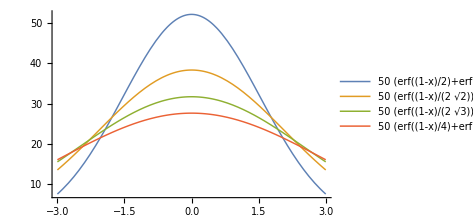

```mathematica
Plot[Evaluate[Table[u2[x,t],{t,4}]],{x,-3,3},PlotLegends->"Expressions",PlotStyle->Thickness[0.003],ImageSize->350]
```

(b) animate.

```mathematica
Manipulate[Plot[Evaluate[u2[x,t],{x,-3,3}],PlotRange->{0,60}],{t,.1,50}]
```

(c) 3D plot.

```mathematica
Plot3D[Evaluate[u2[x,t],{t,0.01,30}],{x,-3,3},PlotRange->{0,80}]
```

-Graphics3D-

2-8 Solution in Integral Form
(1)   (∂u)/(∂t)=c^2(∂^2 u)/(∂x^2)
(6)   u(x,t)=∫_0^∞ u(x,t; p)ⅆp=∫_0^∞ [A(p)cos px+B(p)sin px]ⅇ^(-c^2 p^2 t)ⅆp

Using numbered line (6), p. 569, obtain the solution of numbered line (1), p. 568, in integral form satisfying the initial condition u(x,0)=f(x), where

3. f(x) = 1/(1+x^2)

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=1/(1+x^2)
```

1/(1+x^2)

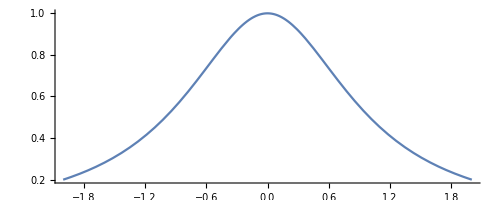

```mathematica
Plot[f[x],{x,-2,2},AspectRatio->Automatic]
```

This function is even. From the procedure of the s.m. in problem 5, I assume this makes the B(p) term in (6) equal to zero, leaving the A(p) term.

```mathematica
aip=2/π∫_0^∞ 1/(1+v^2) Cos[ p v]ⅆv
```

ConditionalExpression[ⅇ^(-Abs[p]),p∈Reals]

The above (green) answer matches the text for the factor A(p). The limits are altered, because the integral does not converge when the original limits are used. However, since the function is even, the limits problem is remedied by using a factor of 2 to mirror the domain around zero. As for the solution form, the absolute value requirement is not observed by the text.

```mathematica
u[x_,t_]=∫_0^∞ ⅇ^(-p-c^2 p^2 t)ⅆp
```

ConditionalExpression[(ⅇ^(1/(4 c^2 t)) √π Erfc[1/(2 √(c^2 t))])/(2 √(c^2 t)),Re[c^2 t]≥0]

The green cell above matches the text answer for u. Considering the limits of the integral, I dropped the absolute value restriction that was on -p. It is interesting to look at the solution form of u, which looks a little congested but still usable.

5. f(x)=|x| if |x|<1 and 0 otherwise

The solution of this problem is included in the s.m., therefore it is the first one worked.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=Piecewise[{{Abs[x],-1<x<1}}]
```

Piecewise[{{Abs[x], -1<x<1}, {0, True}}]

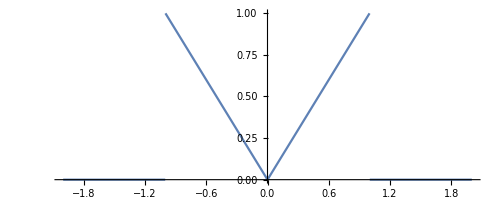

```mathematica
Plot[f[x],{x,-2,2},AspectRatio->Automatic]
```

By inspection, f(x) is even. According to the s.m., this makes the B(p) term in (6) above equal to zero. I didn’t see assumptions which make this necessary, but I did find a resource on line (http://site.iugaza.edu.ps/asakka/files/2014/01/Ch_VI_S.pdf) which says the same thing, so I will accept it.

Numbered line (8) on p. 569 of text allows to calculate A(p):

```mathematica
A[p_]=1/π∫_(-∞)^∞ f[v]Cos[p v]ⅆv
```

(2 (-1+Cos[p]+p Sin[p]))/(p^2 π)

```mathematica
plug=FullSimplify[∫_0^1 ((2 (-1+Cos[p]+p Sin[p]))/(p^2 π))ⅇ^(-c^2 p^2 t)ⅆp]
```

(c √t (2 Erf[c √t]-ⅈ ⅇ^(-1/(4 c^2 t)) (Erfi[(1-2 ⅈ c^2 t)/(2 c √t)]-Erfi[(1+2 ⅈ c^2 t)/(2 c √t)])))/(√π)+(4 ⅇ^(-c^2 t) Sin[1/2]^2)/π

The s.m. announces that the green cell expression is the sought-for answer. It does not quite match the text answer though, which for some reason leaves out the integral sign. The s.m. ignores this omission.

```mathematica
plugn=N[plug/.{c->1}]
```

0.292653 2.71828^(-1. t)+0.56419 √t (2. Erf[√t]-(0.+1. ⅈ) 2.71828^(-0.25/t) (Erfi[(0.5 (1.-(0.+2. ⅈ) t))/(√t)]-1. Erfi[(0.5 (1.+(0.+2. ⅈ) t))/(√t)]))

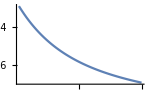

```mathematica
Plot[0.29265264139612696 2.718281828459045^(-1. t)+0.5641895835477563 √t (2. Erf[√t]-(0.+1. ⅈ) 2.718281828459045^(-0.25/t) (Erfi[(0.5 (1.-(0.+2. ⅈ) t))/(√t)]-1. Erfi[(0.5 (1.+(0.+2. ⅈ) t))/(√t)])),{t,0.1,5},ImageSize->150]
```

7. f(x)=(sin x)/x  Hint. Use problem 4 in section 11.7.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=Sin[x]/x
```

Sin[x]/x

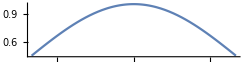

```mathematica
Plot[f[x],{x,-2,2},AspectRatio->0.25, ImageSize->250]
```

This function is even. From the procedure of the s.m. in problem 5, I assume this makes the B(p) term in (6) equal to zero, leaving the A(p) term.

```mathematica
aip=2/π∫_0^∞ Sin[v]/v Cos[ p v]ⅆv
```

ConditionalExpression[1/2 (Sign[1-p]+Sign[1+p]),p∈Reals]

The above (upper green) cell matches the text answer for A(p). Even though the integral exists and converges for the original domain, -∞ to ∞, the text prefers to mirror around zero. The above (lower green) cell matches the intent of the text answer, though the text does not have the Sign function available to express it.

```mathematica
gen=∫_0^∞ aip Cos[ p x] ⅇ^(-c^2 p^2 t)ⅆp;
```

The above yellow cell expresses the general form of u(x,t). However, if the domain extends above 1, aip equals zero, so the whole expression disappears. For p between 0 and 1, aip equals 1. Therefore

```mathematica
u[x,y]=∫_0^1 Cos[ p x] ⅇ^(-c^2 p^2 t)ⅆp;
```

The above green cell matches the answer in the text. As for the hint in the problem description, it is interesting, though not really necessary. Repeating it here:

∫_0^∞ Cos[1/2 π w]/(1-w^2)Cos[x w]ⅆw=Piecewise[{{1/2 π Cos[x], if 0<Abs[x]<1/2 π}, {0, if Abs[x]≥1/2 π}}]

9 - 12 CAS project. Error Function.

(21)     erf=2/(√π)∫_0^x ⅇ^(-w^2)ⅆw

This function is important in applied mathematics and physics (probability theory and statistics, thermodynamics, etc.) and fits our present discussion. Regarding it as a typical case of a special function defined by an integral that cannot be evaluated as elementary calculus, do the following.

9. Graph the bell-shaped curve (the curve of the integrand in (21)). Show that erf is odd. Show that

∫_a^b ⅇ^(-w^2)ⅆw = (√π)/2(erf b - erf a)
∫_-b^b ⅇ^(-w^2)ⅆw=√π erf b

```mathematica
Clear["Global`*"]
```

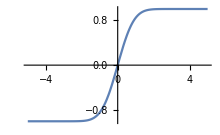

```mathematica
Plot[Erf[x],{x,-5,5}, ImageSize->220]
```

```mathematica
erff[x_,w_]=2/(√π)∫_0^x ⅇ^(-w^2)ⅆw
```

Erf[x]

The yellow cell above shows that Mathematica has recognized the erf function when entered as an anonymous function. By inspection of the plot, the function is odd. I have skipped doing the identities.

10. Obtain the Maclaurin series of erf x from that of the integrand. Use that series to compute a table of erf x for x=0(0.01)3 (meaning x =0,0.01,0.02,...,3).

11. Obtain the values required by problem 10 by in integration command of your CAS. Compare accuracy.

```mathematica
Table[Erf[x],{x,0,1,0.01000000}]
```

{0.,0.0112834,0.0225646,0.0338412,0.0451111,0.056372,0.0676216,0.0788577,0.0900781,0.101281,0.112463,0.123623,0.134758,0.145867,0.156947,0.167996,0.179012,0.189992,0.200936,0.21184,0.222703,0.233522,0.244296,0.255023,0.2657,0.276326,0.2869,0.297418,0.30788,0.318283,0.328627,0.338908,0.349126,0.359279,0.369365,0.379382,0.38933,0.399206,0.409009,0.418739,0.428392,0.437969,0.447468,0.456887,0.466225,0.475482,0.484655,0.493745,0.50275,0.511668,0.5205,0.529244,0.537899,0.546464,0.554939,0.563323,0.571616,0.579816,0.587923,0.595936,0.603856,0.611681,0.619411,0.627046,0.634586,0.642029,0.649377,0.656628,0.663782,0.67084,0.677801,0.684666,0.691433,0.698104,0.704678,0.711156,0.717537,0.723822,0.73001,0.736103,0.742101,0.748003,0.753811,0.759524,0.765143,0.770668,0.7761,0.78144,0.786687,0.791843,0.796908,0.801883,0.806768,0.811564,0.816271,0.820891,0.825424,0.82987,0.834232,0.838508,0.842701}

Accuracy is per-digit-identical compared to an online table. I did not really see the point in going all the way to 3.